### Goal Integrate 1/(√(x - x^2)) with respect to x when 0< x< 1

```mathematica
f[x_]:=1/Sqrt[x-x^2]
```

Assume x > x^2

∫1/(√(x - x^2))ⅆx
= ∫1/(√(-(x^2-  x)))ⅆx
= ∫1/(√(- (x^2 - 2. x . 1/2 + (1/2)^2 - (1/2)^2)))ⅆx
= ∫1/(√(-((x-1/2)^2- 1/4)))ⅆx
= ∫1/(√(1/4 -  (x- 1/2)^2))ⅆx
Let u = x - 1/2 ⇒ ⅆu/ⅆx = 1 ⇒ ⅆu = ⅆx [ Using substitution ]

So, 
∫1/(√(1/4 - u^2))ⅆu
= ArcSin(u/(1/2))
= ArcSin(2 u)
= ArcSin(2(x - 1/2))
= ArcSin(2x - 1)

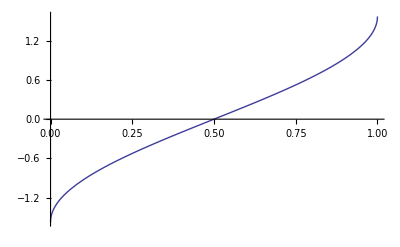

```mathematica
Plot[ArcSin[2x - 1], {x, 0, 1}]
```

## Work-around using ReplaceAll

### In above computation we did following substitution u = x - 1/2 So, in following computation we will replace x with u + 1/2 using ReplaceAll function

```mathematica
sol =Integrate[f[x]/. x-> u+1/2, u]
```

ArcSin[2 u]

Now we can replace u with  x- 1/2

```mathematica
sol/.u->x - 1/2
```

ArcSin[2 (-1/2+x)]

In above evaluation expression inside ArcSin is not simplified. 
So, we can do following to get simplified version.

```mathematica
sol[[1]]
```

2 u

```mathematica
Simplify[sol[[1]]/.u-> x - 1/2]
```

-1+2 x

```mathematica
sol/.sol[[1]]->Simplify[sol[[1]]/.u-> x - 1/2]
```

-ArcSin[1-2 x]

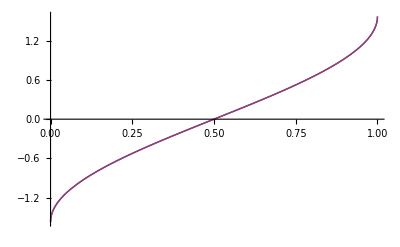

```mathematica
Plot[{- ArcSin[1-2x],ArcSin[2x - 1]}, {x, 0, 1}]
```

```mathematica
{Plot[ArcSin[2x - 1], {x, 0, 1}],Plot[- ArcSin[1-2x], {x, 0, 1}]}
```

{-Graphics-,-Graphics-}